```mathematica
(* Gradient Descent with Modification *)

(* Fitting Function *)
Fitfunction=#2*Exp[#1*#3]+#4&;
varamt=3;

(* Data Generation Settings *)
TrueParams={-2,0.259,1.};
DataLength=100;
SamplingRate=10;
SamplingSet=N[Range[DataLength]]/N[SamplingRate];
NoiseDistribution=NormalDistribution[];
NoiseMagnitude=0.1;

(* Data Generation *)
Noise[x_]:=x*(1.+NoiseMagnitude*RandomVariate[NoiseDistribution]);
DataNoiseless=(Fitfunction@@ #&)/@(Prepend[TrueParams, #]& /@SamplingSet);
Data=Noise/@DataNoiseless;

(*Prep gradient*)
Clear[eFunc,gFunc,params]
params=Table[Unique["p"],{varamt}];
paramh=Hold@@params;
eFunc=paramh/._[vars__]:>Function[{vars},Mean[(((Fitfunction@@Prepend[{vars},#])&/@SamplingSet)-Data)^2]];
gFunc=paramh/._[vars__]:>Function[{vars},Evaluate@Grad[eFunc@@params,params]];

(* Iteration Initialization *)
factor=0.05;
totalIter=0;TotalRefines=0;
velocity={0,0,0};
(*History*)
debugParams={iterParams=initParams={0., 1., 1.}};
```

```mathematica
(*** Iteration Settings ***)

(* Controls - zero fps means that there is NO DELAY *)
doPrint=False;doGraph=False;fps=1./60.;doWarn=False;
doPlot=True;doSpace=True;doEPlot=False;

(** Controls for limiting values **)
err=10000;(*Initialization of error. Start impossible.*)
errorRatio=1.0;(*In what ratio of current error to previous error should it be considered increasing*)
boostRatio=1.2; (*'Impatience' Multiplier to increase factor when error is not increasing*)
refineRatio=0.9;(*'Caution' Multiplier to decrease factor when error is increasing*)
maxRefines=1000;(*Give up refining if refined too many times in a row*)
friction=0.9;

(* Tracker values *)
prevErr=-1;ConsecRefines=0;

(* Iteration Tools Extracted for Compactness *)
ReportIteration[i_]:=If[Mod[i,100]==0 && doPrint,Print["next dir:",dir,"\nnorm:",norm,"\nerr:",err,"\nparams:",iterParams,"\niteration:",i];];
```

```mathematica
(* Realtime monitor plot *)
displayGradient[xV_,yV_]:=Show[ContourPlot[eFunc @@ ReplacePart[iterParams, {xV->x,yV->y}],
{x,iterParams[[xV]]-0.2,iterParams[[xV]]+0.2},{y,iterParams[[yV]]-0.2,iterParams[[yV]]+0.2},
PlotTheme->"Web",AxesLabel->{x,y,z},PlotRange->All,ImageSize->Small],
Graphics[{Blue,PointSize[0.05],Point[{iterParams[[xV]],iterParams[[yV]]}]}]];
(* Visualization of the first 3 function parameters *)
Dynamic[Grid[{{"Data vs Function","Parameter Space","Error over iterations"},
{ListPlot[{(Fitfunction@@Prepend[iterParams,#])&/@SamplingSet,Data},Joined->True,ImageSize->Medium]
,If[varamt==3,If[doGraph,{displayGradient[1,2],displayGradient[2,3],displayGradient[3,1]},
Show[ListPointPlot3D[debugParams,PlotRange->All,ImageSize->Medium],Graphics3D@Line@debugParams],"Non-3 dimensions"]],
If[doEPlot,ListLogPlot[{((eFunc@@#)&)/@debugParams},ImageSize->Medium],"Disabled"]
},
{"Parameters, nGrad, Delta, V","Iterations, factor, corrections"},{Column[{iterParams,-dir,-factor*dir,velocity}],Column[{{totalIter,factor,TotalRefines},ProgressIndicator[ConsecRefines/maxRefines]}],err}
},Frame->All,ItemSize->30]]
```

```mathematica
(*** Iteration loop ***)
(* Iterator and maximum values *)
i=0.;UpperBound=1000.;SmallErr=0.001;prevVelocity={0,0,0};
(* Iteration *)
While[i<UpperBound && err >SmallErr,
(* Determine square difference sum from target for analysis *)
err=eFunc @@ iterParams;
(* Factor Adaptivity - check to see whether error has increased over errorRatio to determine whether to boost or refine *)
If[err/prevErr>errorRatio,
(*If err increased, revert, refine, and retry*)
iterParams=debugParams[[-1]];
velocity=prevVelocity;
If[ConsecRefines>maxRefines,
If[doWarn,Print["Exceeded maximum amount of consecutive corrections."]];Abort[];,
factor*=refineRatio;ConsecRefines++;TotalRefines++;];,
(*Otherwise continue, reset refine counter, and boost*)
prevErr=err;factor*=boostRatio;ConsecRefines=0;];
(* Obtain vector from gradient *)
dir=gFunc @@ iterParams;
(*Report*)ReportIteration[i];(*Pause*)If[fps≠0&&ConsecRefines==0,Pause[fps];];
debugParams=Append[debugParams,iterParams];
velocity-=factor*dir;
velocity*=friction;
prevVelocity=velocity;
iterParams+=velocity;
If[ConsecRefines==0,i++;totalIter++;]
]
```

$Aborted

{4.53373×10^7,1.,1.}

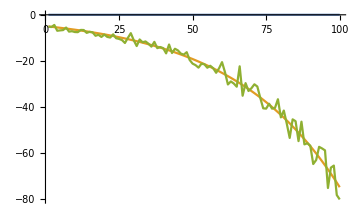

2.78624×10^-29

```mathematica
(***Diagnostic Tools***)

(*Optional Noise Function Plot*)
Plot[Noise[x],{x,0,40},AspectRatio->Full,ColorFunction->Function[{x,y},Hue[Abs[y-x]]]];

(*Parameter History*)
Grid[debugParams[[-10;;-1]]];
Column[eFunc @@ #&/@ debugParams[[-10;;-1]]];
Grid[gFunc @@ #&/@ debugParams[[-10;;-1]]];

(*"Best Parameters" Generated with NMinimize*)
AutoParams=params/.NMinimize[eFunc @@ params,params][[2]];

iterParams-velocity

(*Compare current data, auto-fitted data, and generated data*)
ListPlot[{(Fitfunction@@Prepend[iterParams,#])&/@SamplingSet,(Fitfunction@@Prepend[AutoParams,#])&/@SamplingSet,Data},Joined->True,ImageSize->Medium]

factor
```

```mathematica
iterParams
```

{0.,1.,1.}

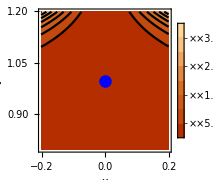
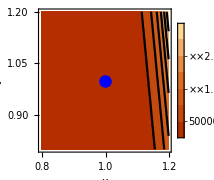
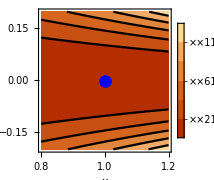

```mathematica
{displayGradient[1,2],displayGradient[2,3],displayGradient[3,1]}
```